First, the various stellar parameters for our two-point model. 
Let’s just start with the first segment, so x_0=0, Δx=h.

```mathematica
xa = 0.5;
xb=1;
h = 1./6.;
Subscript[α, a]=0.5;
Subscript[α, b]=0.;
Subscript[α, aa]=-16.;
Subscript[α, bb]=0.;
```

```mathematica
xc1=xa+h;
xc2=xc1+h;
xb=xc2+h;
t[x_,xi_]:= (x-xi)/ h ;
```

The Cubic Hermit Basis functions

```mathematica
H30[x_,xi_]:=1−3*t[x,xi]^2+2*t[x,xi]^3;
H31[x_,xi_]:=t[x,xi]−2*t[x,xi]^2+t[x,xi]^3;
H32[x_,xi_]:=−t[x,xi]^2+t[x,xi]^3;
H33[x_,xi_]:=3*t[x,xi]^2−2*t[x,xi]^3;
```

```mathematica
Subscript[P, ac1][x_,xi_]:=Subscript[α, a] H30[x,xi]+Subscript[α, aa] h H31[x,xi]+Subscript[α, cc1] h H32[x,xi]+Subscript[α, c1] H33[x,xi];
Subscript[P, c1c2][x_,xi_]:=Subscript[α, c1] H30[x,xi]+Subscript[α, cc1] h H31[x,xi]+Subscript[α, cc2] h H32[x,xi]+Subscript[α, c2] H33[x,xi];
Subscript[P, c2b][x_,xi_]:=Subscript[α, c2] H30[x,xi]+Subscript[α, cc2] h H31[x,xi]+Subscript[α, bb] h H32[x,xi]+Subscript[α, b] H33[x,xi];
```

```mathematica
Subscript[P, ac1][x,xa]
```

-2.66667 (6. (-0.5+x)-72. (-0.5+x)^2+216. (-0.5+x)^3)+0.5 (1-108. (-0.5+x)^2+432. (-0.5+x)^3)+(108. (-0.5+x)^2-432. (-0.5+x)^3) α_c1+0.166667 (-36. (-0.5+x)^2+216. (-0.5+x)^3) α_cc1

```mathematica
Subscript[P, c1c2][x,xc1]
```

(1-108. (-0.666667+x)^2+432. (-0.666667+x)^3) α_c1+(108. (-0.666667+x)^2-432. (-0.666667+x)^3) α_c2+0.166667 (6. (-0.666667+x)-72. (-0.666667+x)^2+216. (-0.666667+x)^3) α_cc1+0.166667 (-36. (-0.666667+x)^2+216. (-0.666667+x)^3) α_cc2

```mathematica
Subscript[P, c2b][x,xc2]
```

0.+(1-108. (-0.833333+x)^2+432. (-0.833333+x)^3) α_c2+0.166667 (6. (-0.833333+x)-72. (-0.833333+x)^2+216. (-0.833333+x)^3) α_cc2

Hydrostatic Mass Conservation

From the stellar structure equations, we see that we can find m^2= -8π(∫_xa^xc x^4*P_ac'*dx+∫_xc^xb x^4*P_cb'*dx), and find P_c in terms of P'_c.

```mathematica
Δm2=-8 Pi*(Integrate[y^4 D[Subscript[P, ac1][y,xa], y],{y,xa,xc1}]+Integrate[y^4 D[Subscript[P, c1c2][y,xc1], y],{y,xc1,xc2}]+Integrate[y^4 D[Subscript[P, c2b][y,xc2], y],{y,xc2,xb}])
```

-8 π (-0.0320755-0.202469 α_c1-0.391975 α_c2-0.00165589 α_cc1-0.00258181 α_cc2)

```mathematica
Δmab = 1.0^2-0.8^2;
```

```mathematica
FullSimplify[Solve[{Δm2==Δmab},{Subscript[α, c1]}]]
```

{{α_c1→-0.0876753-1.93598 α_c2-0.00817847 α_cc1-0.0127516 α_cc2}}

Next,

```mathematica
Subscript[α, c1]=1/(672 h π (h+xa) (7 h^2+10 h xa+5 xa^2))(105 Δmab-24 π (5 h^4+28 h^3 xa+63 h^2 xa^2+70 h xa^3+35 xa^4) Subscript[α, a]-8 h^2 π (4 h^3+21 h^2 xa+42 h xa^2+35 xa^3) Subscript[α, aa]+8 π (3 (1433 h^4+2240 h^3 xa+1323 h^2 xa^2+350 h xa^3+35 xa^4) Subscript[α, b]+h (h (626 h^3+714 h^2 xa+273 h xa^2+35 xa^3) Subscript[α, bb]-84 (2 h+xa) (22 h^2+20 h xa+5 xa^2) Subscript[α, c2]-4 h^2 (23 h^2+42 h xa+21 xa^2) Subscript[α, cc1]-4 h^2 (86 h^2+84 h xa+21 xa^2) Subscript[α, cc2])));
FullSimplify[Subscript[α, c1]]
```

-0.0876753-1.93598 α_c2-0.00817847 α_cc1-0.0127516 α_cc2

```mathematica
FullSimplify[Subscript[P, ac1][xc1,xa]]
```

-0.0876753-1.93598 α_c2-0.00817847 α_cc1-0.0127516 α_cc2

```mathematica
FullSimplify[Subscript[P, c1c2][xc2,xc1]]
```

0.+1. α_c2-3.70074×10^-17 α_cc2

```mathematica
Subscript[dP, ac1][x_]:=FullSimplify[D[Subscript[P, ac1][x,xa], x]];
Subscript[dP, ac1][x]
```

-386.124+(1223.43-966.373 x) x+(836.341+x (-2927.2+2509.02 x)) α_c2+(36.5331+x (-132.366+118.599 x)) α_cc1+(5.50871+x (-19.2805+16.5261 x)) α_cc2

```mathematica
Subscript[dP, c1c2][x_]:=FullSimplify[D[Subscript[P, c1c2][x,xc1], x]];
Subscript[dP, c1c2][x]
```

-(6 (h-x+xa) (2 h-x+xa) α_c2)/h^3+((2 h-x+xa) (4 h-3 x+3 xa) α_cc1)/h^2+((h-x+xa) (5 h-3 x+3 xa) α_cc2)/h^2+1/(112 h^4 π (h+xa) (7 h^2+10 h xa+5 xa^2))(h-x+xa) (2 h-x+xa) (105 Δmab-24 π (5 h^4+28 h^3 xa+63 h^2 xa^2+70 h xa^3+35 xa^4) α_a-8 h^2 π (4 h^3+21 h^2 xa+42 h xa^2+35 xa^3) α_aa+8 π (3 (1433 h^4+2240 h^3 xa+1323 h^2 xa^2+350 h xa^3+35 xa^4) α_b+h (h (626 h^3+714 h^2 xa+273 h xa^2+35 xa^3) α_bb-84 (2 h+xa) (22 h^2+20 h xa+5 xa^2) α_c2-4 h^2 (23 h^2+42 h xa+21 xa^2) α_cc1-4 h^2 (86 h^2+84 h xa+21 xa^2) α_cc2)))

```mathematica
Reduce[{Subscript[dP, ac1][x]<0, 0<xa<x<xb},{Subscript[α, cc1]}]
```

$Aborted

Density

From ρ=m'/(4π x^2),

```mathematica
ρ[x_]:=D[m[y], y]/(4 Pi y^2)/.y->x;
FullSimplify[ρ[x]]
```

m'[x]/(4 π x^2)

Given

```mathematica
Subscript[α, 0]=Subscript[P, 0];
Subscript[α, 1]=Subscript[dP, 0];
Subscript[α, 2]=Subscript[dP, 1];
Subscript[α, 3]=Subscript[P, 1];
x0=0;
h=1;
m20=0;
Subscript[P, 1]=0;
Δm=1;
```

Constraints for Monotonicity

The first constraint involves picking P_0 and dP_0 such that mass is conserved.

```mathematica
m[x]^2
```

8 π (-1/5 x^5 dP_0+(2 x^6 dP_0)/3-(3 x^7 dP_0)/7+(x^6 dP_1)/3-(3 x^7 dP_1)/7+x^6 P_0-(6 x^7 P_0)/7)

```mathematica
newM[x_]:=-8 Pi*( Subscript[P, 0] Integrate[y^4 D[H30[y], y],{y,x0,y}] + Subscript[dP, 0] h   Integrate[y^4 D[H31[y], y],{y,x0,y}] + Subscript[dP, 1] h   Integrate[y^4 D[H32[y], y],{y,x0,y}] + Subscript[P, 1] Integrate[y^4 D[H33[y], y],{y,x0,y}] ) /.y->x ;
newM[x]
```

-8 π ((x^5/5-(2 x^6)/3+(3 x^7)/7) dP_0+(-x^6/3+(3 x^7)/7) dP_1+(-x^6+(6 x^7)/7) P_0)

By inspection, this is the same as m(x). Given m_0 and m_1, we can isolate P_0 in terms of dP_0 plus other constants in order to find the line along which mass and HSE are conserved.

```mathematica
Collect[Solve[{newM[x]==Δm^2},{Subscript[P, 0]}],{Subscript[dP, 0],Subscript[dP, 1]}]
```

{{P_0→-7/(8 π x^6 (-7+6 x))+((-168 π x^5+560 π x^6-360 π x^7) dP_0)/(120 π x^6 (-7+6 x))+((280 π x^6-360 π x^7) dP_1)/(120 π x^6 (-7+6 x))}}

```mathematica
newP1[x_]:=-(7 Δm^2)/(8 π x^6 (-7+6 x))+((-168 π x^5+560 π x^6-360 π x^7) Subscript[dP, 0])/(120 π x^6 (-7+6 x))+((280 π x^6-360 π x^7) Subscript[dP, 1])/(120 π x^6 (-7+6 x))
```

```mathematica
Limit[{newP1[x]},{x->0}]
```

{∞}

Next, we’d like to find the regime of P_0 where  dP < 0 always.

```mathematica
Reduce[{D[P[x], x]< 0 ,Subscript[dP, 0]≤0 , 0<x<1},{Subscript[P, 0]}, Reals]
```

dP_0≤0&&0<x<1&&P_0>(-dP_0+4 x dP_0-3 x^2 dP_0+2 x dP_1-3 x^2 dP_1)/(-6 x+6 x^2)

```mathematica
newP2[x_]:=(-Subscript[dP, 0]+4 x Subscript[dP, 0]-3 x^2 Subscript[dP, 0]+2 x Subscript[dP, 1]-3 x^2 Subscript[dP, 1])/(-6 x+6 x^2)
```

```mathematica
newP2[0.5]
```

-0.666667 (0.25 dP_0+0.25 dP_1)

That should give us dP_0 in terms of dP_1, which is given.

```mathematica
FullSimplify[Solve[{newP1[1/2]==newP2[1/2]},{Subscript[dP, 0]}]]
```

{{dP_0→-560/(3 π)}}

```mathematica
Subscript[dP, 0]=-560/(3 π);
```

```mathematica
Limit[{Subscript[P, 0]=(-Subscript[dP, 0]+4 x Subscript[dP, 0]-3 x^2 Subscript[dP, 0]+2 x Subscript[dP, 1]-3 x^2 Subscript[dP, 1])/(-6 x+6 x^2)},{x->0}]
```

{-∞}

Finally, in order to find the correct Δm^2 (i.e. the correct mass coordinate for dP_0), we minimize d^2 P_0 in the least squares sense. But why? Hmm

```mathematica
Subscript[dP, 1]=0;
Subscript[dP, 0]
P[x]
```

dP_0

(x-2 x^2+x^3) dP_0+(1-3 x^2+2 x^3) P_0

```mathematica
Plot[P[x],{x,0,h}]
```

-Graphics-

First Segment

We can approach this differently from the other cases, since α_1=0 here and it implies something unique about the spline. But what is P_0?

```mathematica
Subscript[α, 1]=0;x0=0;
```

```mathematica
Collect[P[x],x]
```

P_0+x^3 ((2 P_0)/h^3-(2 P_1)/h^3-(m_1 ρ_1)/h^4)+x^2 (-(3 P_0)/h^2+(3 P_1)/h^2+(m_1 ρ_1)/h^3)

```mathematica
Collect[ D[P[x], x], x]
```

x^2 ((6 P_0)/h^3-(6 P_1)/h^3-(3 m_1 ρ_1)/h^4)+x (-(6 P_0)/h^2+(6 P_1)/h^2+(2 m_1 ρ_1)/h^3)

From the stellar structure equations, we see that we can find m^2= (-8π)/a∫_0^x x^4*P'*dx .
However, we just saw that P’ is proportional to x•w, where w is a linear polynomial. 
Then   m^2= x^6*w  , and we choose to write w in linear Hermite form.

```mathematica
H10[x_]:=1-t[x];
H11[x_]:=t[x];
w[x_] := Subscript[β, 0] H10[x]+Subscript[β, 1] H11[x];
```

We can find β_i in terms of α_i.

```mathematica
LHS[x_]:=(-8*Pi)*Integrate[x^4 D[P[x], x],{x,0,x}];
Collect[ LHS[x],x]
```

-8 π x^7 ((6 P_0)/(7 h^3)-(6 P_1)/(7 h^3)-(3 m_1 ρ_1)/(7 h^4))-8 π x^6 (-P_0/h^2+P_1/h^2+(m_1 ρ_1)/(3 h^3))

```mathematica
RHS[x_]:=x^6 w[x];
Collect[RHS[x],x]
```

x^6 β_0+x^7 (-β_0/h+β_1/h)

```mathematica
Solve[{
-8 π x^6 (-Subscript[P, 0]/h^2+Subscript[P, 1]/h^2+(Subscript[m, 1] Subscript[ρ, 1])/(3 h^3))==x^6 Subscript[β, 0],
-8 π x^7 ((6 Subscript[P, 0])/(7 h^3)-(6 Subscript[P, 1])/(7 h^3)-(3 Subscript[m, 1] Subscript[ρ, 1])/(7 h^4))==x^7 (-Subscript[β, 0]/h+Subscript[β, 1]/h)},{Subscript[β, 0],Subscript[β, 1]}]
```

{{β_0→(8 (3 h π P_0-3 h π P_1-π m_1 ρ_1))/(3 h^3),β_1→(8 (3 h π P_0-3 h π P_1+2 π m_1 ρ_1))/(21 h^3)}}

```mathematica
Subscript[β, 0]=(8 (3 h π Subscript[P, 0]-3 h π Subscript[P, 1]-π Subscript[m, 1] Subscript[ρ, 1]))/(3 h^3);
Subscript[β, 1]=(8 (3 h π Subscript[P, 0]-3 h π Subscript[P, 1]+2 π Subscript[m, 1] Subscript[ρ, 1]))/(21 h^3);
```

```mathematica
FullSimplify[w[x]]
```

(8 π (3 h (7 h-6 x) (P_0-P_1)+(-7 h+9 x) m_1 ρ_1))/(21 h^4)

```mathematica
m[x_]:=x^3 w[x]^(1/2)
```

```mathematica
m[x]
```

x^3 √((8 (1-x/h) (3 h π P_0-3 h π P_1-π m_1 ρ_1))/(3 h^3)+(8 x (3 h π P_0-3 h π P_1+2 π m_1 ρ_1))/(21 h^4))

Finally, from stellar structure we see that ρ =m'/(4π x^2)= 3/(4π)w^(1/2)[1+x/6 w'/w]

```mathematica
FullSimplify[-x^2*(D[P[x], x])/m[x]]
```

(√(21/(2 π)) (6 h (h-x) (P_0-P_1)+(-2 h+3 x) m_1 ρ_1))/(2 h^4 √((3 h (7 h-6 x) (P_0-P_1)+(-7 h+9 x) m_1 ρ_1)/h^4))

```mathematica
ρ[x_]:=(√(21/(2 π)) (6 h (h-x) (Subscript[P, 0]-Subscript[P, 1])+(-2 h+3 x) Subscript[m, 1] Subscript[ρ, 1]))/(2 h^4 √((3 h (7 h-6 x) (Subscript[P, 0]-Subscript[P, 1])+(-7 h+9 x) Subscript[m, 1] Subscript[ρ, 1])/h^4))
```

But we still don’t have enough information. What is P_0? Is there a way we can find it?

```mathematica
m[h]
```

2 √(2/21) h^3 √((3 h π P_0-3 h π P_1+2 π m_1 ρ_1)/h^3)

```mathematica
Reduce[{ρ[x]>0 ,0<x<h , m[x]>0},{Subscript[P, 0]} ]
```

(ρ_1|P_1)∈Reals&&x>0&&h>x&&((m_1<0&&((ρ_1≤0&&P_0>(21 h^2 P_1-18 h x P_1+7 h m_1 ρ_1-9 x m_1 ρ_1)/(21 h^2-18 h x))||(ρ_1>0&&P_0>(6 h^2 P_1-6 h x P_1+2 h m_1 ρ_1-3 x m_1 ρ_1)/(6 h^2-6 h x))))||(m_1==0&&P_0>(21 h^2 P_1-18 h x P_1)/(21 h^2-18 h x))||(m_1>0&&((ρ_1<0&&P_0>(6 h^2 P_1-6 h x P_1+2 h m_1 ρ_1-3 x m_1 ρ_1)/(6 h^2-6 h x))||(ρ_1≥0&&P_0>(21 h^2 P_1-18 h x P_1+7 h m_1 ρ_1-9 x m_1 ρ_1)/(21 h^2-18 h x)))))

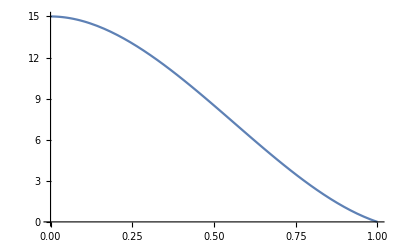

```mathematica
Plot[P[x],{x,0,h}]
```